```mathematica
SetDirectory[NotebookDirectory[]];
mat2 = Import["Displacements9.txt","Table"];
```

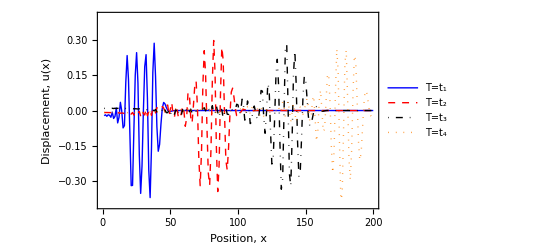

```mathematica
A=ListPlot[{mat2[[All,160]],mat2[[All,360]],mat2[[All,570]],mat2[[All,730]]},Joined->True,PlotRange-> {-0.4,0.4},AspectRatio->1/GoldenRatio,PlotStyle->{Blue,Directive[Dashed,Red,Thick],Directive[DotDashed,Black],Directive[Dotted,Orange]},Frame->True,FrameLabel-> {"Position, x","Displacement, u(x)"},PlotLegends->Placed[LineLegend[{Blue,Directive[Dashed,Red,Thick],Directive[DotDashed,Black,Thick],Directive[Dotted,Orange,Thick]},{"T=t_1","T=t_2","T=t_3","T=t_4"}],Right],BaseStyle->{FontFamily->"Times",16}]
```

```mathematica
Export["medium_wave_propagation.pdf",A]
```

medium_wave_propagation.pdf

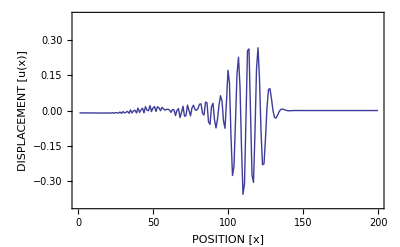

```mathematica
B = ListPlot[{mat2[[All,480]]},Joined->True,PlotRange-> {-0.4,0.4},Frame->True,FrameLabel-> {"POSITION [x]","DISPLACEMENT [u(x)]"}]
```

```mathematica
Export["wave.pdf",B]
```

wave.pdf

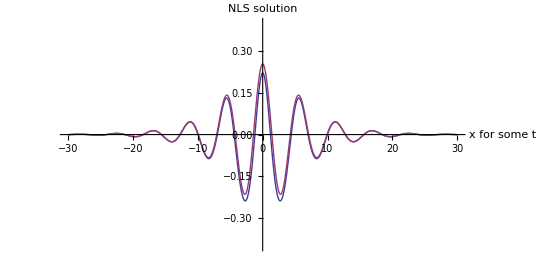

45/128

```mathematica
co =√10;
ω = 2;
q = (√(ω^2-1))/co;
vg = (q co^2)/ω;
P = (co^2-vg^2)/(2ω);
Q = 9/(8ω);
ue = 0.7;
up =0.3;
ϕo = √((ue^2-2ue up)/(2 P Q));
Le = 1/ϕo √((2 P)/Q);
κ= ue/(2P);
μ = (ue up)/(2 P);
ϵ = 0.8;
ξ1[x_,t_] :=  (x-vg t);
τ2[t_] := t;
Am[x_,t_] := ϕo Sech[(ξ1[x,t]-ue τ2[t])/Le]Exp[ⅈ (κ ξ1[x,t]-μ τ2[t])]
disp[x_,t_] :=  Re[ϵ Am[x,t]Exp[ⅈ(q x-ω t)]+0.25 ϵ^2 Am[x,t]^2 Exp[ⅈ 2(q x-ω t)]-0.75Abs[ϵ^2 Am[x,t]^2]]
d[x_,t_] := ϵ ϕo Sech[(ξ1[x,t]-ue τ2[t])/Le]Cos[κ ξ1[x,t]-μ τ2[t]+q x-ω t]
Plot[{disp[x,0],d[x,0]},{x,-30,30},PlotRange-> {-0.4,0.4}, AxesLabel-> {"x for some t", "NLS solution"}, AspectRatio-> 0.5]
P Q
```

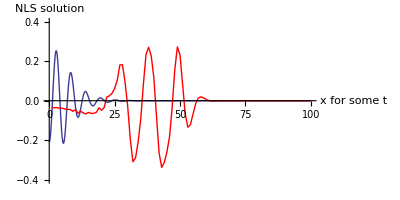

```mathematica
i=5;
Show[Plot[d[x-1,0.1i],{x,0,100},PlotRange-> {-0.4,0.4}, AxesLabel-> {"x for some t", "NLS solution"}, AspectRatio-> 0.5], ListPlot[mat2[[All,200]],PlotJoined->True,PlotRange-> {-0.4,0.4}, PlotStyle-> Red,AxesLabel-> {x,Displacement},PlotLabel->"Phonon (Numerical) Propagation"]]
```

```mathematica
plots = Table[ListPlot[mat2[[All,i]],PlotJoined->True,PlotRange-> {-0.4,0.4}],{i,1,1000}];
```

```mathematica
Manipulate[ListPlot[mat2[[All,i]],PlotJoined->True,PlotRange-> {-0.4,0.4}],{i,1,100}];
```

```mathematica
ListAnimate[plots]
```

```mathematica
Export["medium_amplitude_animation.avi",plots]
```

medium_amplitude_animation.avi

```mathematica
theory = Table[Plot[disp[x,i],{x,-10,70},PlotRange-> {-0.2,0.2}],{i,1,20}];
```

```mathematica
Manipulate[Plot[d[x,i],{x,0,70},PlotRange-> {-0.4,0.4}],{i,0,20}]
```

```mathematica
FullSimplify[N[d[x,0]]]
```

0.185903 Cos[0.+1.26772 x] Sech[0.+0.415692 x]

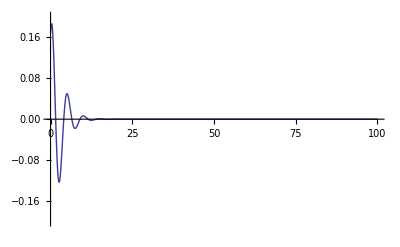

```mathematica
Plot[0.185903 Cos[0.4187801207018599-1.26772 x]* 2/(Exp[0.15125429320954945-0.415692x]+Exp[-0.15125429320954945+0.415692x]),{x,0,100},PlotRange->{-0.2,0.2}]
```

```mathematica
N[d[0,t]]
```

0.185903 Cos[4.1878 t] Sech[1.51254 t]

```mathematica
N[D[d[0,t],t]]
```

-0.778526 Sech[1.51254 t] Sin[4.1878 t]-0.281187 Cos[4.1878 t] Sech[1.51254 t] Tanh[1.51254 t]

```mathematica
N[D[D[d[0,t],t],t]]
```

-3.26031 Cos[4.1878 t] Sech[1.51254 t]-0.425307 Cos[4.1878 t] Sech[1.51254 t]^3+2.35511 Sech[1.51254 t] Sin[4.1878 t] Tanh[1.51254 t]+0.425307 Cos[4.1878 t] Sech[1.51254 t] Tanh[1.51254 t]^2

```mathematica
N[d[x,0]]
```

0.185903 Cos[0.+1.26772 x] Sech[0.415692 (0.+x)]

```mathematica
N[D[d[x,t],t]/.t->0]
```

-0.778526 Sech[0.415692 (0.+x)] Sin[0.-1.26772 x]+0.281187 Cos[0.-1.26772 x] Sech[0.415692 (0.+x)] Tanh[0.415692 (0.+x)]

```mathematica
FullSimplify[N[D[D[d[x,t],t],t]]/.t->0]
```

Sech[0.+0.415692 x] (Cos[0.-1.26772 x] (-3.26031-0.425307 Sech[0.+0.415692 x]^2)-2.35511 Sin[0.-1.26772 x] Tanh[0.+0.415692 x]+0.425307 Cos[0.-1.26772 x] Tanh[0.+0.415692 x]^2)

```mathematica
F[i_]:= Abs[Fourier[mat2[[All,i]]]];
```

```mathematica
Y[k_]:= Table[F[k][[i]],{i,100}]
Z=Table[(2π i)/100,{i,1,100}];
```

```mathematica
fourierplots = Table[ListPlot[Thread[{Z,Y[i]}],PlotJoined->True,PlotRange-> {-0.35,0.35}, AxesLabel-> {"Frequency(ω)","|H(ω)|"}],{i,1,600}];
```

```mathematica
ListAnimate[fourierplots]
```

```mathematica
u[x_,t_] := 10Sech[x-0.6Cos[x-2t]t]
```

```mathematica
ListAnimate[Table[Plot[Cos[x-2t],{x, 0,100},PlotRange-> {-1.5,1.5}],{t,1,100}]]
```

```mathematica
G = {a,b,c,e};
```

```mathematica
G[[4]]
```

e

```mathematica
Table[G[[i]],{i,3}]
```

{a,b,c}

```mathematica
Abort[]
```

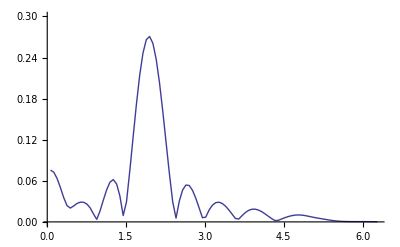

```mathematica
ListPlot[Thread[{Z,Y[180]}], PlotJoined-> True, PlotRange->{0, 0.3}]
```

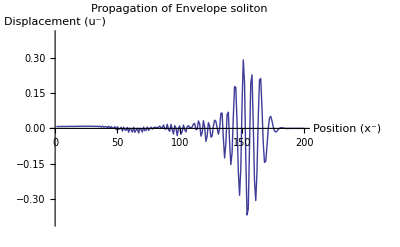

```mathematica
ListPlot[mat2[[All,640]],PlotJoined->True,PlotRange-> {-0.4,0.4},AxesLabel-> {"Position (x^-)","Displacement (u^-)"},PlotLabel->"Propagation of Envelope soliton"]
```

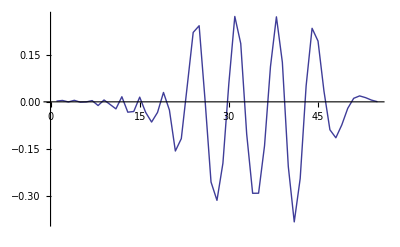

```mathematica
ListPlot[Table[mat2[[i,180]],{i,55}], PlotJoined-> True]
```

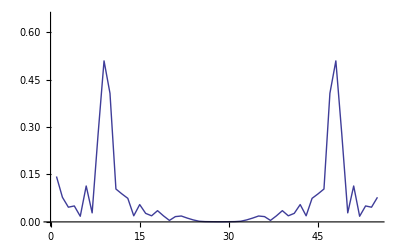

```mathematica
ListPlot[Abs[Fourier[Table[mat2[[i,180]],{i,55}]]], PlotJoined-> True, PlotRange->{0,0.65}]
```

```mathematica
Z1=Table[(2π i)/30,{i,1,60}];
```

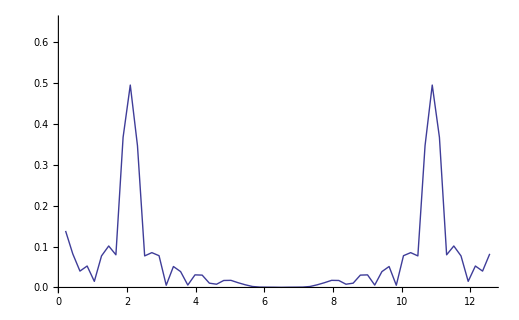

```mathematica
ListPlot[Thread[{Z1,Abs[Fourier[Table[mat2[[i,180]],{i,60}]]]}], PlotJoined-> True, PlotRange->{0,0.65}]
```

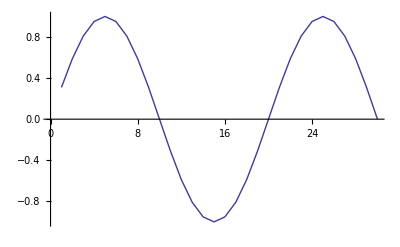

```mathematica
data=Table[N[Sin[6Pi n/60]],{n,30}];
ListLinePlot[data]
```

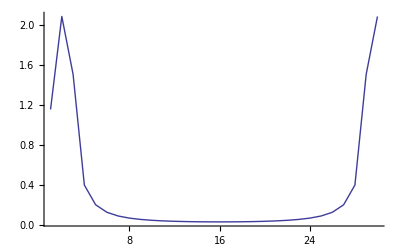

```mathematica
ListLinePlot[Abs[Fourier[data]], PlotRange -> All]
```

```mathematica
For[i=0,i<10,i++,data2 =Prepend[data2,0]]
```

```mathematica
data2
```

{0,0,0,0,0,0,0,0,0,0,0,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,0.,-0.309017,-0.587785,-0.809017,-0.951057,-1.,-0.951057,-0.809017,-0.587785,-0.309017,0.,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,0.,-0.309017,-0.587785,-0.809017,-0.951057,-1.,-0.951057,-0.809017,-0.587785,-0.309017,0.,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,0.,-0.309017,-0.587785,-0.809017,-0.951057,-1.,-0.951057,-0.809017,-0.587785,-0.309017,0.,0.309017,0.587785,0.809017,0.951057,1.,0.951057,0.809017,0.587785,0.309017,0.,-0.309017,-0.587785,-0.809017,-0.951057,-1.,-0.951057,-0.809017,-0.587785,-0.309017,0.}

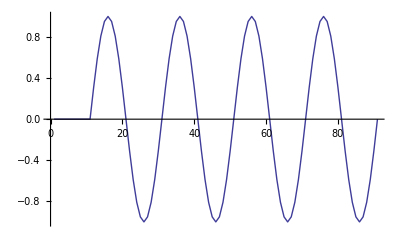

```mathematica
ListLinePlot[data2]
```

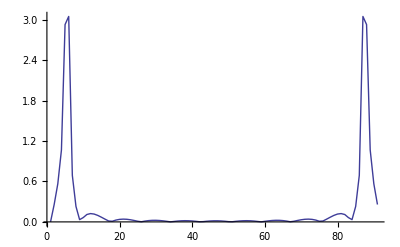

```mathematica
ListPlot[Abs[Fourier[data2]], PlotJoined-> True, PlotRange->All]
```

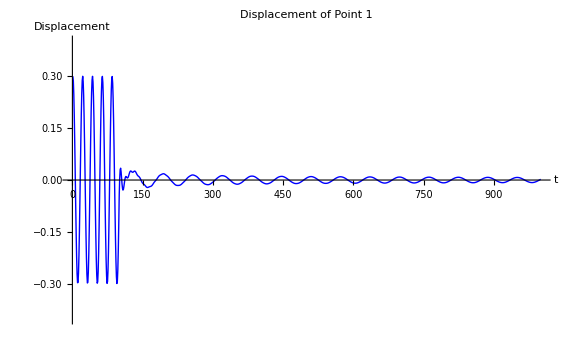

```mathematica
ListPlot[mat2[[1,All]],PlotJoined->True,PlotRange-> {-0.4,0.4}, PlotStyle-> Blue,AxesLabel-> {t,Displacement},PlotLabel->"Displacement of Point 1"]
```

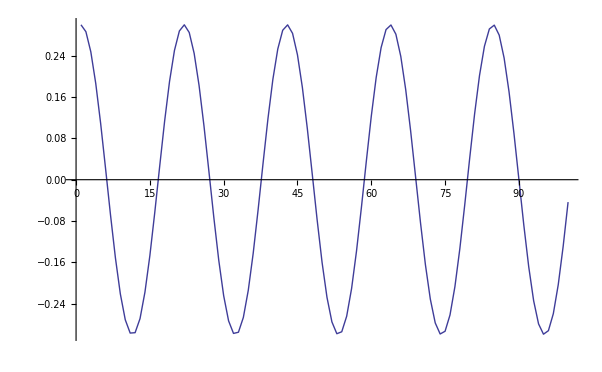

```mathematica
ListPlot[Table[mat2[[1,i]],{i,100}], PlotJoined-> True]
```

```mathematica
(2π)/2.1
```

2.99199

```mathematica
NSolve[w[x]== 2,x]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-0.554811},{x→0.554811}}